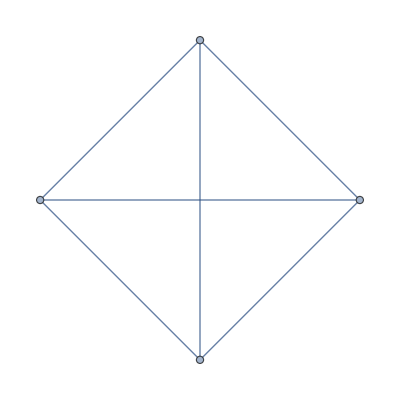

```mathematica
ReadGrof[1]
```

```mathematica
Block[{i,max,g,START=200000,ALL=10000,result={}},
Monitor[
For[i=START+1,i≤START+ALL,i++,
g=ReadGrof[i];
max=Fold[And,Table[VertexDegree[g,v]==5,{v,VertexList[g]}]];
If[max,
AppendTo[result,g]
]
]
,Row[{i,ProgressIndicator[(i-START)/ALL],START+ALL}]
];
result
]
```

{}

```mathematica
allGraphs4[280,"colofour"]
```

v13x24+v13x2x4+v1x24x3+v1x2x3x4